## Import astro

/Users/cmccabe/Downloads/AtMolDM-main/Neon/dRdE

/Users/cmccabe

InterpolatingFunction[…]

2.62585×10^-10

0.

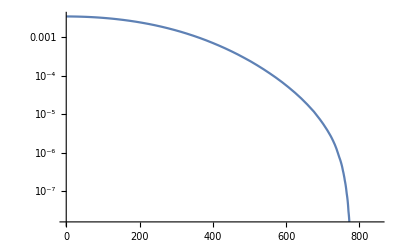

```mathematica
SetDirectory[NotebookDirectory[]]
Lgvmin=Import["gvmin_round.dat"];
ResetDirectory[]
fgvmin=Interpolation[Lgvmin,InterpolationOrder->1]
fgvmin[779]
fgvmin[780]

LogPlot[fgvmin[vmin],{vmin,0,850}]
```

## Import fion

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

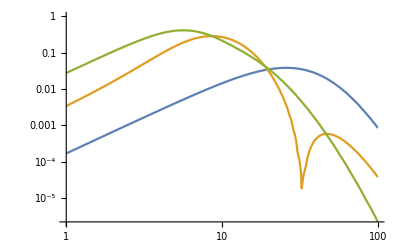

```mathematica
(*set path to form factor files*)
SetDirectory[NotebookDirectory[]<>"../Formfactor_HX"];
(*set path to form factor files*)

L1s=Import["Ne1s_Sch_grid.dat"];
L2s=Import["Ne2s_Sch_grid.dat"];
L2p=Import["Ne2p_Sch_grid.dat"];
ResetDirectory[];

f1s=Interpolation[L1s,InterpolationOrder->1]
f2s=Interpolation[L2s,InterpolationOrder->1]
f2p=Interpolation[L2p,InterpolationOrder->1]

LogLogPlot[{f1s[qx,0.02],f2s[qx,0.02],f2p[qx,0.02]},{qx,1,100}]
```

## Parameters

```mathematica
Params1s=Association[
wnl->2,
Inl->870.2,
fionnl->f1s
];

Params2s=Association[
wnl->2,
Inl->48.5,
fionnl->f2s
];

Params2p=Association[
wnl->6,
Inl->21.7,
fionnl->f2p
];
```

## Rate calculation: FDM = 1

σe40 is the cross section relative to 10^-40 cm^2

#### dR/dE calculation: FDM = 1

```mathematica
TdRdE[mDMMeV0_,MNGeV0_,σe40_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

ρ=0.3;(*GeV cm^-3*)
σe=10^-40 σe40a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=779;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=  ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM=1

```mathematica
TdRETotal[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1s=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1s],InterpolationOrder->1];
fσ2s=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2s],InterpolationOrder->1];
fσ2p=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2p],InterpolationOrder->1];

Ftot[x_]:=fσ1s[x]+fσ2s[x]+fσ2p[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

```mathematica
TdREComponents[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1s=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1s],InterpolationOrder->1];
fσ2s=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2s],InterpolationOrder->1];
fσ2p=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2p],InterpolationOrder->1];

EikeV=0.001;
EfkeV=1.0;
steps=250;

T1=Table[{10^log10ErkeV,fσ1s[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T2=Table[{10^log10ErkeV,fσ2s[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T3=Table[{10^log10ErkeV,fσ2p[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

{T1,T2,T3}
]
```

### Calculate and Plot

```mathematica
ANe=20.18;
MNGeV=ANe .931494; (*GeV*)
σ1=1; (*10^-40cm^2 cross section*)

TR30MeV=TdRETotal[30,MNGeV,σ1];
TR300MeV=TdRETotal[300,MNGeV,σ1];
TR1000MeV=TdRETotal[1000,MNGeV,σ1];

Tcomponents30MeV=TdREComponents[30,MNGeV,σ1];
Tcomponents300MeV=TdREComponents[300,MNGeV,σ1];
Tcomponents1000MeV=TdREComponents[1000,MNGeV,σ1];

(*SetDirectory[NotebookDirectory[]];
Export["dRdE_Ne_30MeV.dat",TR30MeV]
Export["dRdE_Ne_300MeV.dat",TR300MeV]
Export["dRdE_Ne_1000MeV.dat",TR1000MeV]
ResetDirectory[];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {47.2399}. NIntegrate obtained 0.135148 and 4.34801×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {44.4286}. NIntegrate obtained 0.134555 and 4.31559×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {39.231}. NIntegrate obtained 0.133943 and 3.12716×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {29.7973703471425}. NIntegrate obtained 0.219719 and 0.0000625547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {29.8157242318774}. NIntegrate obtained 0.219359 and 0.0000637721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {29.8349435904918}. NIntegrate obtained 0.218989 and 0.0000649442 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {1006.85}. NIntegrate obtained 0.0000163758 and 6.32193×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {1006.86}. NIntegrate obtained 0.0000163633 and 6.31593×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {1006.88}. NIntegrate obtained 0.0000163497 and 6.30443×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {47.2399}. NIntegrate obtained 0.135148 and 4.34801×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {44.4286}. NIntegrate obtained 0.134555 and 4.31559×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {39.231}. NIntegrate obtained 0.133943 and 3.12716×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {29.7973703471425}. NIntegrate obtained 0.219719 and 0.0000625547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {29.8157242318774}. NIntegrate obtained 0.219359 and 0.0000637721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {29.8349435904918}. NIntegrate obtained 0.218989 and 0.0000649442 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {1006.85}. NIntegrate obtained 0.0000163758 and 6.32193×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {1006.86}. NIntegrate obtained 0.0000163633 and 6.31593×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {1006.88}. NIntegrate obtained 0.0000163497 and 6.30443×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

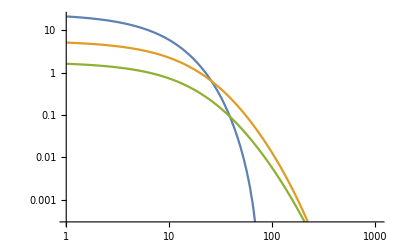

```mathematica
(*convert x-axis to eV*)
TR30MeV[[All,1]]=10^3 TR30MeV[[All,1]];
TR300MeV[[All,1]]=10^3 TR300MeV[[All,1]];
TR1000MeV[[All,1]]=10^3 TR1000MeV[[All,1]];


Show[ListLogLogPlot[{TR30MeV,TR300MeV,TR1000MeV},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```

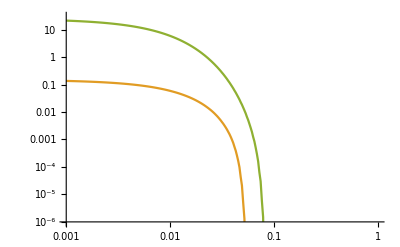

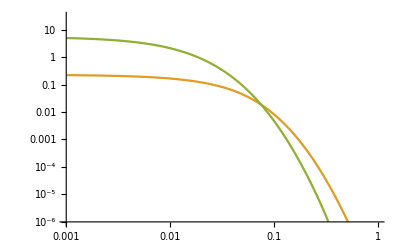

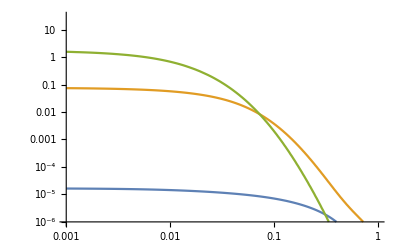

```mathematica
ListLogLogPlot[Tcomponents30MeV,Joined->True,PlotRange->{{10^-3,1},{ 10^-6,30}}]
ListLogLogPlot[Tcomponents300MeV,Joined->True,PlotRange->{{10^-3,1},{10^-6,30}}]
ListLogLogPlot[Tcomponents1000MeV,Joined->True,PlotRange->{{10^-3,1},{10^-6,30}}]
```

## Rate calculation: FDM = (alpha me / q)^2

σe37 is the cross section relative to 10^-37 cm^2

#### dR/dE calculation: FDM = (alpha me / q)^2

```mathematica
TdRdElightmed[mDMMeV0_,MNGeV0_,σe37_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

αEM=1/137.04;
ρ=0.3;(*GeV cm^-3*)
σe=10^-37 σe37a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
mekeV=1000. meMeV;(*keV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=779;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

FDM[qkeV_]:=(αEM mekeV/qkeV)^2;

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=   FDM[qkeV]^2ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM = (alpha me / q)^2

```mathematica
TdRETotallightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1s=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1s],InterpolationOrder->1];
fσ2s=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2s],InterpolationOrder->1];
fσ2p=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2p],InterpolationOrder->1];

Ftot[x_]:=fσ1s[x]+fσ2s[x]+fσ2p[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

```mathematica
TdREComponentslightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1s=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1s],InterpolationOrder->1];
fσ2s=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2s],InterpolationOrder->1];
fσ2p=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2p],InterpolationOrder->1];

EikeV=0.001;
EfkeV=1.0;
steps=250;

T1=Table[{10^log10ErkeV,fσ1s[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T2=Table[{10^log10ErkeV,fσ2s[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T3=Table[{10^log10ErkeV,fσ2p[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

{T1,T2,T3}
]
```

### Calculate and Plot

```mathematica
ANe=20.18;
MNGeV=ANe .931494; (*GeV*)
σ1=1; (*10^-37cm^2 cross section*)

TR30MeVlightmed=TdRETotallightmed[30,MNGeV,σ1];
TR300MeVlightmed=TdRETotallightmed[300,MNGeV,σ1];
TR1000MeVlightmed=TdRETotallightmed[1000,MNGeV,σ1];

Tcomponents30MeVlightmed=TdREComponentslightmed[30,MNGeV,σ1];
Tcomponents300MeVlightmed=TdREComponentslightmed[300,MNGeV,σ1];
Tcomponents1000MeVlightmed=TdREComponentslightmed[1000,MNGeV,σ1];

(*SetDirectory[NotebookDirectory[]];
Export["dRdE_Ne_30MeV_lightmed.dat",TR30MeVlightmed]
Export["dRdE_Ne_300MeV_lightmed.dat",TR300MeVlightmed]
Export["dRdE_Ne_1000MeV_lightmed.dat",TR1000MeVlightmed]
ResetDirectory[];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {25.273707276531826249055256994324736297130584716796875}. NIntegrate obtained 0.00460419 and 4.61237×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {24.0274033030401914512452776762074790894985198974609375}. NIntegrate obtained 0.0045658 and 6.0569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {24.053174510144097464348078574403189122676849365234375}. NIntegrate obtained 0.00452657 and 9.38281×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {526.429}. NIntegrate obtained 2.4491×10^-13 and 2.96284×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {526.476}. NIntegrate obtained 2.44444×10^-13 and 2.77581×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {540.006}. NIntegrate obtained 2.33957×10^-13 and 3.07914×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {501.499541330826758667171816341578960418701171875}. NIntegrate obtained 1.59195×10^-11 and 4.62273×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {501.519288763722585144932963885366916656494140625}. NIntegrate obtained 1.59049×10^-11 and 4.46133×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {501.539967063951081627237726934254169464111328125}. NIntegrate obtained 1.58892×10^-11 and 4.43771×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {25.273707276531826249055256994324736297130584716796875}. NIntegrate obtained 0.00460419 and 4.61237×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {24.0274033030401914512452776762074790894985198974609375}. NIntegrate obtained 0.0045658 and 6.0569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {24.053174510144097464348078574403189122676849365234375}. NIntegrate obtained 0.00452657 and 9.38281×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {526.429}. NIntegrate obtained 2.4491×10^-13 and 2.96284×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {526.476}. NIntegrate obtained 2.44444×10^-13 and 2.77581×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {540.006}. NIntegrate obtained 2.33957×10^-13 and 3.07914×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {501.499541330826758667171816341578960418701171875}. NIntegrate obtained 1.59195×10^-11 and 4.62273×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {501.519288763722585144932963885366916656494140625}. NIntegrate obtained 1.59049×10^-11 and 4.46133×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {501.539967063951081627237726934254169464111328125}. NIntegrate obtained 1.58892×10^-11 and 4.43771×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

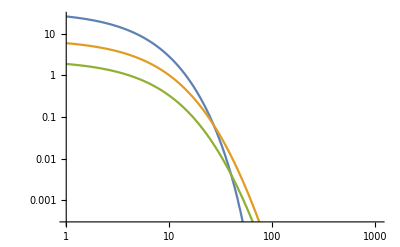

```mathematica
(*convert x-axis to eV*)
TR30MeVlightmed[[All,1]]=10^3 TR30MeVlightmed[[All,1]];
TR300MeVlightmed[[All,1]]=10^3 TR300MeVlightmed[[All,1]];
TR1000MeVlightmed[[All,1]]=10^3 TR1000MeVlightmed[[All,1]];


Show[ListLogLogPlot[{TR30MeVlightmed,TR300MeVlightmed,TR1000MeVlightmed},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```

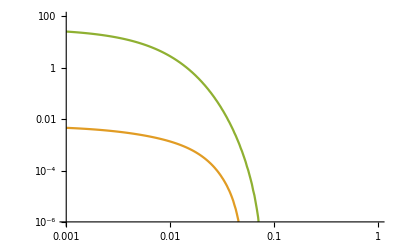

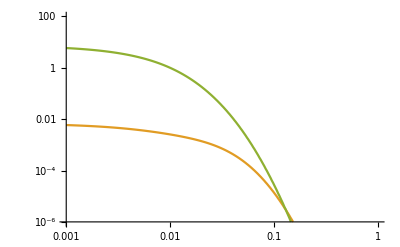

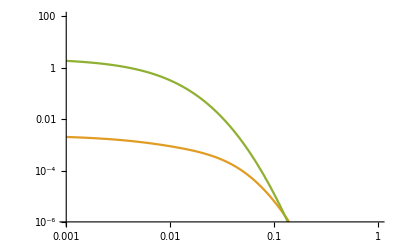

```mathematica
ListLogLogPlot[Tcomponents30MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{10^-6,100}}]
ListLogLogPlot[Tcomponents300MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{10^-6,100}}]
ListLogLogPlot[Tcomponents1000MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{10^-6,100}}]
```